```mathematica
Options[svgExport]={"CommentString"->"Created by Mathematica",AspectRatio->Automatic,Background->Automatic};
Clear[svgExport];
svgExport[name_String,gr_,opts:OptionsPattern[]]:=Module[{svgCode=StringReplace[ExportString[First@ImportString[ExportString[gr,"PDF",Background->OptionValue[Background]],"PDF"],"SVG",Background->OptionValue[Background]],"<svg "->"<svg "<>If[OptionValue[AspectRatio]===Full," preserveAspectRatio='none' "," "]]&[ToString/@ImageDimensions[Rasterize[Show[gr,ImagePadding->0],"Image"]]]},Export[name,StringReplace[svgCode,RegularExpression["(<svg\\b[^>]*>)"]:>"$1"<>"\n<!-- ***Exported Comment***\n"<>OptionValue["CommentString"]<>"\n***Exported Comment*** -->"],"Text"]]

edges = {1<->2,1<->3,3<->4,3<->5,5<->6,5<->7,7<->8};
coords = {{0,0},{0,-1},{1,0},{1,-1},{2,0},{2,-1},{3,0},{3,-1}};
names = {1,1,2,2,3,3,4,4};
Graph[edges, VertexCoordinates->coords,VertexSize->Medium,ImageSize->400,
VertexLabels->Thread[Range[8]->(Placed[Style[#,12,"Panel",Background->None],Center]&/@names)]]
```

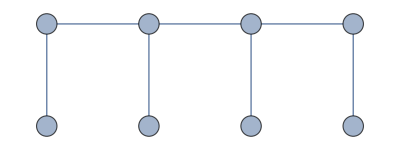

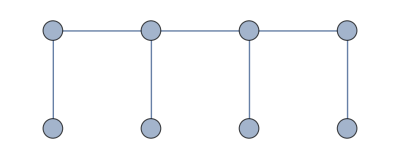
```mathematica
svgExport["/Users/elvis/Documents/DSI/courses/content/graphical-models/images/hmm_graph_example_2.svg",-Graphics-, AspectRatio->Full]
```

/Users/elvis/Documents/DSI/courses/content/graphical-models/images/hmm_graph_example_2.svg

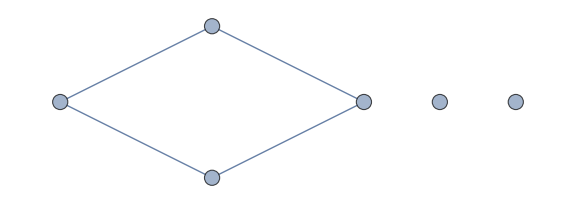

```mathematica
edges = {3<->5};
coords = {{2,1},{0,0},{2,-1},{4,0},{5,0},{6,0}};
g1 = Graph[Range@6,{1<->2,2<->3,3<->4,1<->4}, VertexSize->Medium,ImageSize->Large,
VertexLabels->Placed["Name",Center], VertexCoordinates->coords]
```

```mathematica
svgExport["/Users/elvis/Documents/DSI/courses/content/graphical-models/images/minimal_graph_ex_1.svg",g1,AspectRatio->Full]
```

/Users/elvis/Documents/DSI/courses/content/graphical-models/images/minimal_graph_ex_1.svg

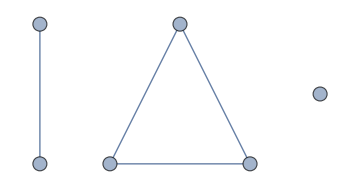

```mathematica
edges = {1<->2,3<->4,4<->5,3<->5};
coords = {{0,0},{0,-2},{2,0},{1,-2},{3,-2},{4,-1}};
g2 = Graph[Range@6, edges, VertexSize->Medium,ImageSize->Medium,
VertexLabels->Placed["Name",Center], VertexCoordinates->coords]
```

```mathematica
svgExport["/Users/elvis/Documents/DSI/courses/content/graphical-models/images/indep_rule_ex_1.svg",g2,AspectRatio->Full]
```

/Users/elvis/Documents/DSI/courses/content/graphical-models/images/indep_rule_ex_1.svg

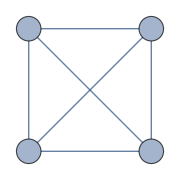

```mathematica
edges = {1<->2,1<->3,2<->3,3<->4,3<->5,4<->5};
coords = {{0,0},{0,-2},{1,-1},{2,0},{2,-2}};
g3 = Graph[edges, VertexSize->Medium,ImageSize->Small,
VertexLabels->Placed["Name",Center], VertexCoordinates->coords];
edges = {1<->2,1<->3,1<->4,3<->4,2<->4,2<->3};
coords = {{0,0},{0,-2},{2,0},{2,-2}};
names = {1,2,4,5};
g4 = Graph[edges, VertexCoordinates->coords,VertexSize->Medium,ImageSize->Small,
VertexLabels->Thread[Range[4]->(Placed[Style[#,12,"Panel",Background->None],Center]&/@names)]]
```

```mathematica
svgExport["/Users/elvis/Documents/DSI/courses/content/graphical-models/images/marginal_rule_ex_1.svg",g4,AspectRatio->Full]
```

/Users/elvis/Documents/DSI/courses/content/graphical-models/images/marginal_rule_ex_1.svg

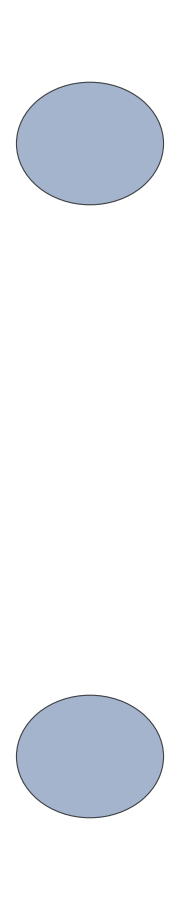

```mathematica
coords = {{0,0},{0,-2}};
names = {1,3};
g4 = Graph[Range@2,{},VertexSize->Medium,ImageSize->Small,
VertexLabels->Thread[Range[2]->(Placed[Style[#,12,"Panel",Background->None],Center]&/@names)]]
```

```mathematica
svgExport["/Users/elvis/Documents/DSI/courses/content/graphical-models/images/indep_exercise_1.svg",g4,AspectRatio->Full]
```

/Users/elvis/Documents/DSI/courses/content/graphical-models/images/indep_exercise_1.svg

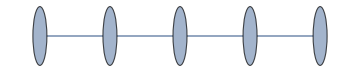

```mathematica
edges = {1<->2,1<->3,3<->6,2<->5};
coords = {{0,0},{0,-2},{1,-1},{2,0},{2,-2}};
g6 = Graph[edges, VertexSize->Medium,ImageSize->Medium,
VertexLabels->Placed["Name",Center]]
```

```mathematica
svgExport["/Users/elvis/Documents/DSI/courses/content/graphical-models/images/indep_exercise_3.svg",g6,AspectRatio->Full]
```

/Users/elvis/Documents/DSI/courses/content/graphical-models/images/indep_exercise_3.svg

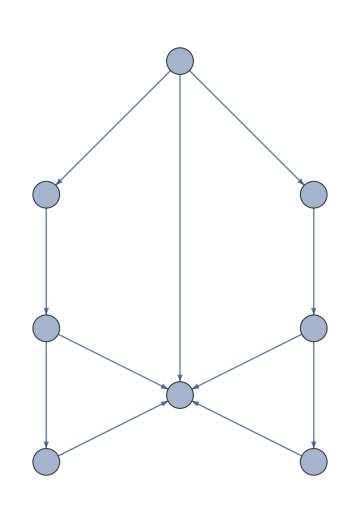

{1,2,3,6,4,5,7,8}

```mathematica
edges = {1->2,1->3,1->6,2->4,3->5,4->6,4->7,5->6,5->8,7->6,8->6};
coords = {{1,0},{0,-1},{2,-1},{1,-2.5},{0,-2},{2,-2},{0,-3},{2,-3}};
g7 = Graph[edges, VertexCoordinates->coords,VertexSize->Medium,ImageSize->Medium,VertexLabels->Placed["Name",Center]]
VertexList[g7]
```

```mathematica
AcyclicGraphQ[g7]
```

True

```mathematica
svgExport["/Users/elvis/Documents/DSI/courses/content/graphical-models/images/directed_acyclic_graph_ex_1.svg",g7,AspectRatio->Full]
```

/Users/elvis/Documents/DSI/courses/content/graphical-models/images/directed_acyclic_graph_ex_1.svg

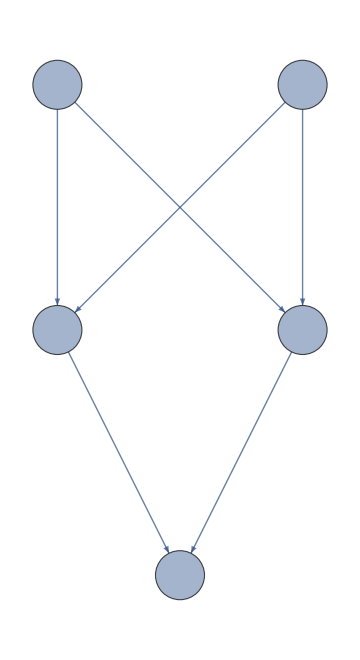

{1,3,4,2,5}

```mathematica
edges = {1->3,1->4,2->3,2->4,3->5,4->5};
coords = {{0,0},{0,-1},{1,-1},{1,0},{0.5,-2}};
g8 = Graph[edges,VertexCoordinates->coords,VertexSize->Medium,ImageSize->Medium,VertexLabels->Placed["Name",Center]]
VertexList[g8]
```

```mathematica
svgExport["/Users/elvis/Documents/DSI/courses/content/graphical-models/images/bn_ex_1.svg",g8,AspectRatio->Full]
```

/Users/elvis/Documents/DSI/courses/content/graphical-models/images/bn_ex_1.svg

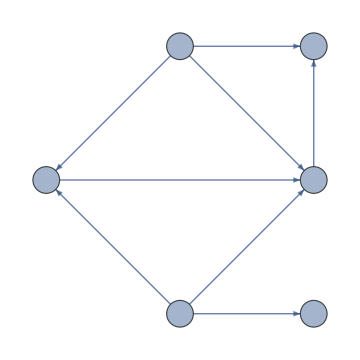

{1,2,3,4,5,6}

```mathematica
edges = {1->2,1->3,1->4,2->4,4->3,5->2,5->4,5->6};
coords = {{1,0},{0,-1},{2,0},{2,-1},{1,-2},{2,-2}};
g8 = Graph[edges,VertexCoordinates->coords, VertexSize->Medium,ImageSize->Medium,VertexLabels->Placed["Name",Center]]
VertexList[g8]
```

```mathematica
svgExport["/Users/elvis/Documents/DSI/courses/content/graphical-models/images/bn_indep_ex_1.svg",g8,AspectRatio->Full]
```

/Users/elvis/Documents/DSI/courses/content/graphical-models/images/bn_indep_ex_1.svg

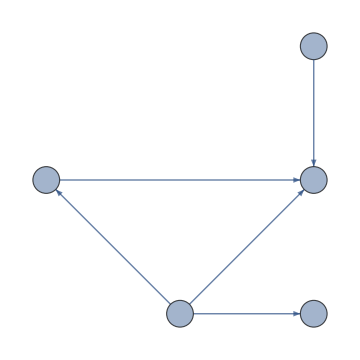

{1,3,2,4,5}

```mathematica
edges = {1->3,2->3,4->1,4->3,4->5};
coords = {{0,-1},{2,-1},{2,0},{1,-2},{2,-2}};
names = {2,3,4,5,6};
g9 = Graph[edges,VertexCoordinates->coords, VertexSize->Medium,ImageSize->Medium,VertexLabels->Thread[Range[5]->(Placed[Style[#,12,"Panel",Background->None],Center]&/@names)]]
VertexList[g9]
```

```mathematica
svgExport["/Users/elvis/Documents/DSI/courses/content/graphical-models/images/bn_cond_ex_1.svg",g9,AspectRatio->Full]
```

/Users/elvis/Documents/DSI/courses/content/graphical-models/images/bn_cond_ex_1.svg

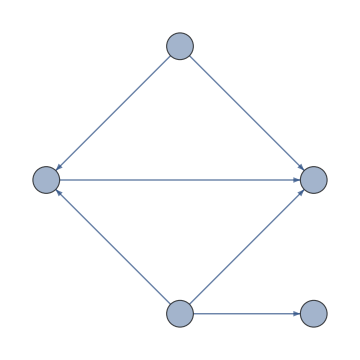

{1,2,3,4,5}

```mathematica
edges = {1->2,1->3,2->3,4->2,4->3,4->5};
coords = {{1,0},{0,-1},{2,-1},{1,-2},{2,-2}};
names = {1,2,4,5,6};
g10 = Graph[edges,VertexCoordinates->coords, VertexSize->Medium,ImageSize->Medium,VertexLabels->Thread[Range[5]->(Placed[Style[#,12,"Panel",Background->None],Center]&/@names)]]
VertexList[g10]
```

```mathematica
svgExport["/Users/elvis/Documents/DSI/courses/content/graphical-models/images/bn_marginal_ex_1.svg",g10,AspectRatio->Full]
```

/Users/elvis/Documents/DSI/courses/content/graphical-models/images/bn_marginal_ex_1.svg

```mathematica
edges = {1->2,1->3,3->4,3->5,5->6,5->7,7->8};
coords = {{0,0},{0,-1},{1,0},{1,-1},{2,0},{2,-1},{3,0},{3,-1}};
names = {1,1,2,2,3,3,4,4};
Graph[edges, VertexCoordinates->coords,VertexSize->Medium,ImageSize->400,
VertexLabels->Thread[Range[8]->(Placed[Style[#,12,"Panel",Background->None],Center]&/@names)]]
```